# Ghrelin dynamics

#### Data

```mathematica
dataghrelin= {{0,625.29},{1,650.48},{2,626.89},{3,613.66},{4,542.79},{5,504.43},{6,501.48},{7,600.55},{8,704.07},{8.5,525.29},{9,321.37},{9.5,343.57},{10,352.47},{10.5,345.11},{11,389.49},{11.5,450.11},{12,648.17},{12.5,689.58},{13,432.47},{13.5,451.71},{14,422.18},{14.5,408.92},{15,502.05},{15.5,484.35},{16,509.51},{16.5,540.58},{17,691.34},{17.5,704.68},{18,639.68},{18.5,514.1},{19,515.61},{19.5,450.62},{20,492.03},{20.5,475.81},{21,602.93},{22,608.91},{23,608.97}};
```

## Insulin fit with ghrelin model

### Parameters

```mathematica
{k12,k2x,σ,khx,β,β2,γ,ρ}={2.30,0.71,0.20,2.354,1591,1238,1.29,80};
```

### Equations

Parameters θ, δ, ϕ/Kix  for insulin dynamics are unknown

```mathematica
patron[t_,r_]:=If[8<t<8.65,r,If[12<t<12.41,r,If[17.5<t<17.90,r,0]]];

GH[gh_,gl2_,t_]:=If[0<=t<3||6<=t<24,β,β2]/(1+γ gl2)-khx  gh;
GL2[gl1_,gl2_]:=k12/(1+σ gl2) gl1-k2x  gl2;
GL1[gl1_,gl2_]:=-(gl1  k12)/(1+σ gl2);
```

### Solving equation for ghrelin dynamics

```mathematica
ghrelin=NDSolve[{
g1'[t]==GL1[g1[t],g2[t]]+patron[t,2.1],
g2'[t]==GL2[g1[t],g2[t]],
h1'[t]==GH[h1[t],g2[t],t],
g1[0]== 0,g2[0]==0.01,h1[0]==400},{g1[t],g2[t],h1[t],in[t]},{t,2,24}];
```

#### Plotting Insulin daily dynamics

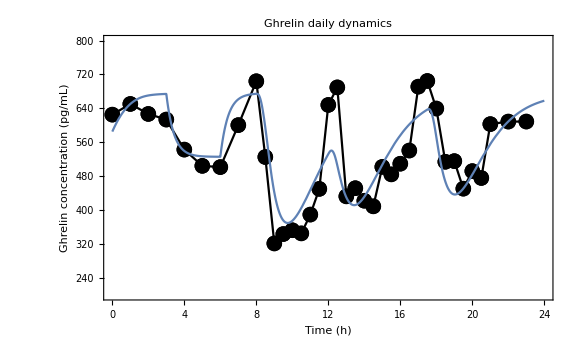

```mathematica
ghrelin=Show[ListLinePlot[dataghrelin,PlotStyle->Black,Mesh->Full],Plot[Evaluate[h1[t]/. ghrelin],{t,0,24},PlotRange->{200,800},Filling->{2->{1}}],FrameTicks->{{All,None},{{0,4,8,12,16,20,24},None}},RotateLabel->True,PlotRange->{200,800},Frame->True,PlotLabel->"Ghrelin daily dynamics",ImageSize->Large,LabelStyle->{15,GrayLevel[0],Bold},FrameLabel->{"Time (h)","Ghrelin concentration (pg/mL)"}]
```

# Fit for insulin dynamics

#### Longer raw data for representation

```mathematica
datainsulin= {{0,120.83},{1,113.24},{2,106.86},{3,103.65},{4,90.16},{5,79.23},{6,79.44},{7,89.17},{8,89.17},{8.5,71.34},{9.5,391.79},{10,518.51},{10.5,502.54},{11,373.14},{11.5,331.01},{12,214.13},{12.5,168.69},{13,384.29},{13.5,341.9},{14.5,248.41},{15,244.37},{15.5,154.12},{16,199.26},{16.5,155.32},{17,170.29},{17.5,126.07},{18,144.55},{18.5,280.14},{19,382.17},{19.5,393.84},{20,349.66},{20.5,292.61},{21,222.61},{21.5,188.44},{22,159.02},{23,129.76}};
```

#### Shorter raw data for fitting

```mathematica
datainsulinsimplified = {{0,120.83},{1,113.24},{2,106.86},{3,103.65},{4,90.16},{5,79.23},{6,79.44},{7,89.17},{8,71.34},{9,518.51},{9.5,502.54},{10,373.14},{11,214.13},{12,113.44},{13,341.9},{14,248.41},{15,154.12},{16,155.32},{17,126.07},{18,280.14},{19,393.84},{20,428.12},{21,288.44},{22,209.02},{23,169.76}};
```

## Insulin fit with ghrelin model

### Parameters

```mathematica
{k12,k2x,σ,khx,β,β2,γ,ρ}={2.30,0.71,0.20,2.354,1591,1238,1.29,80};
```

### Equations

Parameters θ, δ, ϕ/Kix  for insulin dynamics are unknown

```mathematica
patron[t_,r_]:=If[8<t<8.65,r,If[12<t<12.41,r,If[17.5<t<17.90,r,0]]];
IN[gl2_,In_]:=ρ+(θ gl2^m)/(δ^m+gl2^m)-ϕ In;
GH[gh_,gl2_,t_]:=If[0<=t<3||6<=t<24,β,β2]/(1+γ gl2)-khx  gh;
GL2[gl1_,gl2_]:=k12/(1+σ gl2) gl1-k2x  gl2;
GL1[gl1_,gl2_]:=-(gl1  k12)/(1+σ gl2);
```

### Fitting using NonlinearModelFit

```mathematica
m=4;
pfun2=ParametricNDSolveValue[{
g1'[t]==GL1[g1[t],g2[t]]+patron[t,2.1],
g2'[t]==GL2[g1[t],g2[t]],
h1'[t]==GH[h1[t],g2[t],t],
in'[t]==IN[g2[t],in[t]],
g1[0]== 0,g2[0]==0.01,h1[0]==400, in[0]==120.83},in,{t,0,23},{θ,δ,ϕ }];
fit = NonlinearModelFit[datainsulinsimplified,pfun2[θ,δ,ϕ ][t],{{θ,800},{δ,0.32},{ϕ ,1.5}},t,MaxIterations->Infinity];
```

#### Statistic

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
θ | 528.627 | 161.366 | 3.27595 | 0.00345343
δ | 0.378277 | 0.128951 | 2.9335 | 0.0076898
ϕ | 1.02588 | 0.300677 | 3.41191 | 0.00249923

#### Plotting Insulin daily dynamics

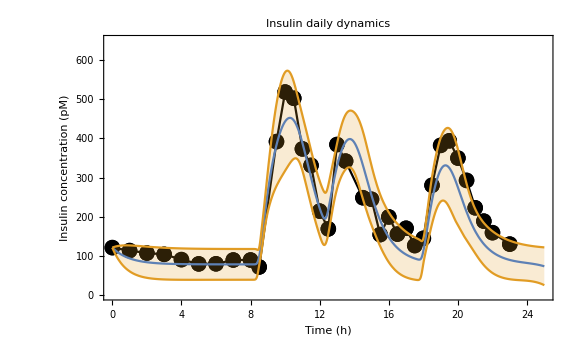

```mathematica
bands90[x_]=fit["MeanPredictionBands",ConfidenceLevel->.90];
Show[ListLinePlot[datainsulin,PlotStyle->Black,Mesh->Full],Plot[{fit[t],bands90[t]},{t,0,25},Filling->{2->{1}}],FrameTicks->{{All,None},{{0,4,8,12,16,20,24},None}},RotateLabel->True,PlotRange->{0,650},Frame->True,PlotLabel->"Insulin daily dynamics",ImageSize->Large,LabelStyle->{15,GrayLevel[0],Bold},FrameLabel->{"Time (h)","Insulin concentration (pM)"}]
```

# Fit for leptin dynamics

#### Raw data

```mathematica
dataleptin={{0,22.8286},{1,23.4473},{2,23.503},{3,23.5769},{4,23.9776},{5,23.9425},{6,23.2717},{7,22.6371},{8,22.5111},{8.5,21.0934},{9,19.4697},{9.5,17.1366},{10,16.0502},{10.5,15.6503},{11,15.9026},{11.5,16.3265},{12,16.6017},{12.5,17.3575},{13,17.0149},{13.5,17.9537},{14,16.3524},{14.5,17.7032},{15,17.7882},{15.5,18.0114},{16,18.506},{16.5,19.7699},{17,19.8795},{17.5,20.316},{18,20.7525},{18.5,21.298},{19,20.6447},{19.5,19.6463},{20,19.774},{20.5,20.0834},{21,20.2112},{22,21.1926},{23,21.393}};
```

## leptin fit with insulin+ghrelin model

### Parameters

```mathematica
{θ,δ,s,ϕ}={528.63,0.38,4,1.03};
```

```mathematica
{FM,BV,max}={60000,5000,24};
```

### Equations

Parameters R, EC50, and ϵ/Klpx  for leptin dynamics are unknown

```mathematica
LP[lepp_,λ_]:=(( FM((R*max)/(1+((λ/EC50)^l))) -ϵ lepp )/BV);
```

### Fitting using NonlinearModelFit

```mathematica
l = 1;
pfun2=ParametricNDSolveValue[{
g1'[t]==GL1[g1[t],g2[t]]+patron[t,2.1],
g2'[t]==GL2[g1[t],g2[t]],
h1'[t]==GH[h1[t],g2[t],t],
in'[t]==IN[g2[t],in[t]],
lep'[t]==LP[lep[t],in[t]],
g1[0]== 0,g2[0]==0.01,h1[0]==400, in[0]==120.83,lep[0]==22.82},lep,{t,0,23},{R ,EC50,ϵ}];
fit2 = NonlinearModelFit[dataleptin,pfun2[R,EC50,ϵ][t],{{R,0.03},{EC50,101},{ϵ,5697.14}},t,MaxIterations->Infinity];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

#### Statistic

```mathematica
fit2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
R | 0.109955 | 0.0212917 | 5.16424 | 0.0000105167
EC50 | 661.119 | 77.8386 | 8.49347 | 6.40629×10^-10
ϵ | 6231.39 | 1243.34 | 5.0118 | 0.0000165834

#### Plotting leptin daily dynamics

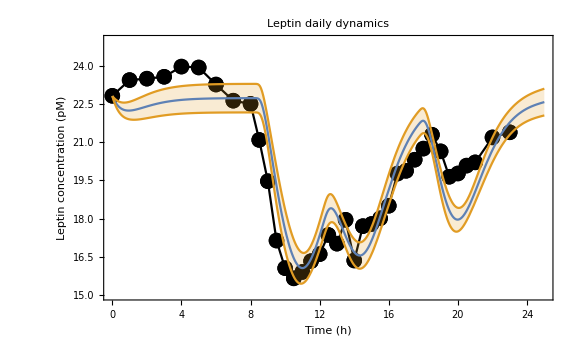

```mathematica
bands902[x_]=fit2["MeanPredictionBands",ConfidenceLevel->.90];
Show[ListLinePlot[dataleptin,PlotStyle->Black,Mesh->Full],Plot[{fit2[t],bands902[t]},{t,0,25},Filling->{2->{1}}],FrameTicks->{{All,None},{{0,4,8,12,16,20,24},None}},RotateLabel->True,PlotRange->{15,25},Frame->True,PlotLabel->"Leptin daily dynamics",ImageSize->Large,LabelStyle->{15,GrayLevel[0],Bold},FrameLabel->{"Time (h)","Leptin concentration (pM)"}]
```

MC4R fitting parameters

### Principal Currents

I_l_i=g_l_i (V_n-E_l);

```mathematica
Il[V_]:=gl(V-El);
```

I_Na_i=g_Na_i a_Na_i(V_n-E_Na),a_Na_i=a_(Na_∞) , a_(Na_∞)=1/(1+Exp[-S_Na(V_n-V_(0Na))]);

```mathematica
INa[aNa_,V_]:=gNa aNa (V-ENa); aNa∞[V_]:=1/(1+Exp[-SNa(V-V0Na)]);
```

I_K_i=g_K_i a_K_i(V_n-E_K),(ⅆ a_K_i)/ⅆt=(a_(K_∞)-a_K_i)/τ_K,a_(K_∞)=1/(1+Exp[-S_K(V_n-V_(0K))]);

```mathematica
IK[aK_,V_]:=gK aK (V-EK);aK[aK∞_,aK_]:=(aK∞-aK)/τK;aK∞[V_]:=1/(1+Exp[-SK(V-V0K)]);
```

### Circadian rhythm

I_circadian=Ac(0.97 Sin[wc t]+ 0.22 Sin[2 wc t]+0.07 Sin[3 wc t]+0.03 Sin[4 wc t]+0.001 Sin[5 wc t]+1)

```mathematica
Icircadian[t_,wc_,Ac_]:=Ac*(0.97*Sin[wc*t-Pi/3]+0.22*Sin[2*wc*t-Pi/3]+0.07*Sin[3*wc*t-Pi/3]+0.03*Sin[4*wc*t-Pi/3]+0.001Sin[5*wc*t-Pi/3]+1);
```

### Calculate RaMC4R parameters

#### MC4R

I_MC4R=g_MC4R a_MC4R(V_n-E_MC4R),RaMC4R=((C_αMSH+T_α(1+C_AgRP/T_A))/(T_α((1+m )+(1/T_A+m/Z_A)C_AgRP)+(1+(m T_α)/Z_α) C_αMSH)),C_relase_i=1/(1+Exp[-S_syn(V_n-V_spike)]),C_cleft_i= C_relase_i/τ_acomulation-C_cleft_i/τ_elimination,a_MC4R=RaMC4R/τ_activation-a_MCR/τ_inactivation;

```mathematica
IMC4R[V_,aMC4R_]:=gMC4R aMC4R(V-EMC4R);Ccleft[Crelase_,Ccleft_]:= Crelase/τacoαMSH-Ccleft/τeliαMSH;
Ccleft2[Crelase_,Ccleft_]:= Crelase/τacoAgRP-Ccleft/τeliAgRP;
Crelase[V_,max_]:=max/(1+Exp[-Ssyn(V-Vspike)]);
RaMC4R[αMSH_,AgRP_,Tα_,Zα_,TA_,ZA_]:=(αMSH+Tα(1+AgRP/TA))/(Tα ((1+m)+(1/TA+m/ZA) AgRP)+(1+(m Tα)/Zα) αMSH);
aMC4R[RaMC4R_,aMC4R_]:=RaMC4R/τactMC4R-aMC4R/τinacMC4R;
KK[kapp_,max_]:=(kapp*basal)/max;
Lx=(1-basal)/basal;
kk[kapp_,max_]:=(KK[kapp,max]*Lx*max)/(1-max);
```

### Parameters

```mathematica
{gMC4R,EMC4R,Ssyn,Vspike,τacoαMSH,τeliαMSH,τacoAgRP,τeliAgRP,τactMC4R,τinacMC4R}={0.1,-38,1,-20,400,300,300,300,734.4,2030.4};
```

```mathematica
{gl,El,gNa,ENa,SNa,V0Na,gK,EK,SK,V0K,τK}={0.1,-60,3,50,0.25,-25,4,-90,0.25,-25,2};
```

```mathematica
{basal,m}={0.5,1};
Grid[{{"AgRP",SpanFromLeft,SpanFromLeft,"MSH",SpanFromLeft,SpanFromLeft},{"k*","L","k","k*","L","k"},{TA=KK[3.6*^-9,0.1],Lx,ZA=kk[3.6*^-9,0.1],Tα=KK[0.16*^-9,0.9],Lx,Zα=kk[0.16*^-9,0.9]}},Frame->All]
```

AgRP |  |  | MSH |  | 
k* | L | k | k* | L | k
1.8×10^-8 | 1. | 2.×10^-9 | 8.88889×10^-11 | 1. | 8.×10^-10

### Simulation

```mathematica
Metabotropic={
V'[t]==-Il[V[t]]-INa[aNa∞[V[t]],V[t]]-IK[aKV[t],V[t]]-IMC4R[V[t],AMC4R[t]],
A'[t]==-Il[A[t]]-INa[aNa∞[A[t]],A[t]]-IK[aKA[t],A[t]]+Iext[t],
P'[t]== -Il[P[t]]-INa[aNa∞[P[t]],P[t]]-IK[aKP[t],P[t]]+Iext2[t],
L'[t]==-Il[L[t]]-INa[aNa∞[L[t]],L[t]]-IK[aKL[t],L[t]]-IMC4R[L[t],AMC4R[t]]+Icircadian[t,0.000073,0.045],
aKV'[t]== aK[aK∞[V[t]],aKV[t]],
aKA'[t]==aK[aK∞[A[t]],aKA[t]],
aKP'[t]==aK[aK∞[P[t]],aKP[t]],
aKL'[t]==aK[aK∞[L[t]],aKL[t]],
αMSH'[t]== Ccleft[Crelase[P[t],1*^-9],αMSH[t]],
AgRP'[t]== Ccleft2[Crelase[A[t],1*^-8],AgRP[t]],
AMC4R'[t]== aMC4R[RaMC4R[αMSH[t],AgRP[t],Tα,Zα,TA,ZA],AMC4R[t]],
V[0]== -60,A[0]== -60,P[0]==-60,L[0]==-60,aKV[0]==0,aKA[0]==0,aKP[0]==0,aKL[0]==0,αMSH[0]==0,AgRP[0]==0,AMC4R[0]==1.38};
```

#### Input

```mathematica
control3 = {Iext[0]==0.9,WhenEvent[Mod[t,15000],Iext[t]->0]};
```

```mathematica
control4 = {Iext2[0]==0,WhenEvent[Mod[t,6000],Iext2[t]->0.9]};
```

#### Solution to ODEs

```mathematica
sol={V[t],A[t],P[t],L[t],aKV[t],aKA[t],aKP[t],aKL[t],αMSH[t],AgRP[t],AMC4R[t]}/.NDSolve[{Metabotropic,control3,control4},{V,A,P,L,aKV,aKA,aKP,aKL,αMSH,AgRP,AMC4R},{t,0,20000},DiscreteVariables->{Iext,Iext2}]/.t-> Range[0,20000,0.01];
```

#### Plots

```mathematica
n=20;
```

```mathematica
plot3=ListLinePlot[{sol[[1]][[11]]},PlotRange->All,Frame->True,FrameTicks->{{{All},{{1.30,"1.30"},{1.40,"1.40"},{1.50,"1.50"}}},{{0,4,8,12,16,20},None}},FrameLabel->{"Time (s)","aMC4R"},DataRange->{0,n},ImageSize->Medium,LabelStyle->{15,GrayLevel[0],Bold},AspectRatio->1/3];
```

```mathematica
plot1=ListLinePlot[{sol[[1]][[9]]*1*^9},PlotRange->All,Frame->True,FrameLabel->{None,"αMSH (nM)"},DataRange->{0,n},ImageSize->Medium,LabelStyle->{15,GrayLevel[0],Bold},AspectRatio->1/3,FrameTicks->{{{All},{{0,"0.00"},0.010,0.020}},{{None},None}},PlotLabel->"MC4R activity"];
```

```mathematica
plot2=ListLinePlot[{sol[[1]][[10]]*1*^9},PlotRange->All,Frame->True,FrameLabel->{None,"AgRP (nM)"},DataRange->{0,n},ImageSize->Medium,LabelStyle->{15,GrayLevel[0],Bold},AspectRatio->1/3,FrameTicks->{{{All},{{0.00,"0.00"},{0.15,"0.15"},{0.30,"0.30"}}},{{None},None}}];
```

```mathematica
b3=Grid[{
{plot1},{plot2},{plot3}
}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Export["figureS1a.jpeg",b3,ImageResolution->600];
```